### Start choosing the example:

```mathematica
t=23;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EliminatorX: Good job!

DataToEquations: Done.

{0.096958,Null}

```mathematica
v0=MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

#### Non-linear case

```mathematica
alpha = 0;
beta = 0;
A = 0.2;
Parameters["alpha"] = alpha;
Parameters
```

<|alpha→0,beta→0,g[m]→Log,W[x,A]→Function[{x,a},a Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$8004[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$8004[x$]-g$8004[m$]]|>

```mathematica
MFGEquations["Nrhs"]
```

{j118-j123+Intg[j118-j123],j119-j124+Intg[j119-j124],j120-j125+Intg[j120-j125]}

```mathematica
FixedSolverStepX1[MFGEquations]@ MFGEquations["criticalreduced1"][[2]]//KeySort
```

Possible multiple solutions 
{False,<|j122→1,u150→2,j119→1/3,j121→1,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u145→2,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u151→8/3,j118→1/3,j120→0,j123→0,u142→8/3,u143→7/3,u144→2,u146→8/3|>}

<|j122→1,u150→2,j119→1/3,j121→1,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u145→2,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u151→8/3,j118→1/3,j120→0,j123→0,u142→8/3,u143→7/3,u144→2,u146→8/3|>

{}

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

```mathematica
FixedSolverStepX1[MFGEquations]@%//KeySort
```

Possible multiple solutions 
{False,<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>}

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

{}

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]]//N,11, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

Possible multiple solutions 
{False,<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>}

<|j122→1.,u150→2.,j119→0.333333,j121→1.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u145→2.,u147→2.33333,u148→2.,u149→2.66667,u151→2.66667,j118→0.333333,j120→0.,j123→0.,u142→2.66667,u143→2.33333,u144→2.,u146→2.66667|>

{}

<|j118→0.333333,j119→0.333333,j120→0.,j121→1.,j122→1.,j123→0.,j124→0.,j125→0.666667,j126→0.,j127→0.,jt128→0.,jt129→0.,jt130→0.,jt131→0.,jt132→0.333333,jt133→0.666667,jt134→0.333333,jt135→0.,jt136→0.,jt137→0.333333,jt138→0.,jt139→0.666667,jt140→0.,jt141→0.,u142→2.66667,u143→2.33333,u144→2.,u145→2.,u146→2.66667,u147→2.33333,u148→2.,u149→2.66667,u150→2.,u151→2.66667|>

```mathematica
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol1
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol2
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol3n
```

0.153654

√(Abs[-u142+u147-Intg[j118-j123]]^2+Abs[-u143+u148-Intg[j119-j124]]^2+Abs[-u144+u149-Intg[j120-j125]]^2)

√(Abs[-u142+u147-Intg[j118-j123]]^2+Abs[-u143+u148-Intg[j119-j124]]^2+Abs[-u144+u149-Intg[j120-j125]]^2)

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

EqEliminartorX2: Count!

The system is False. Returning the inputs.

EqEliminartorX2: Count!

The system is False. Returning the inputs.

FixedX2: next step: j118-j123-u142+u147==j118-j123+Intg[j118-j123]&&j119-j124-u143+u148==1. j118-1. j123+Intg[1. j118-1. j123]&&j120-j125-u144+u149==-1.+1. j118-1. j123+Intg[-1.+1. j118-1. j123]

$Aborted

```mathematica
nsol3n=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest->(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

The system is False. Returning the inputs.

FixedX3: next step: j118-j123-u142+u147==j118-j123+Intg[j118-j123]&&j119-j124-u143+u148==1. j118-1. j123+Intg[1. j118-1. j123]&&j120-j125-u144+u149==-1.+1. j118-1. j123+Intg[-1.+1. j118-1. j123]

Throw::nocatch: Uncaught Throw[<|j122→1,u150→2,j119→1/3,j121→1,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u145→2,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u151→8/3,j118→1/3,j120→0,j123→0,u142→8/3,u143→7/3,u144→2,u146→8/3|>] returned to top level.

Hold[Throw[<|j122→1,u150→2,j119→1/3,j121→1,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u145→2,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u151→8/3,j118→1/3,j120→0,j123→0,u142→8/3,u143→7/3,u144→2,u146→8/3|>]]

### What is this plot for?

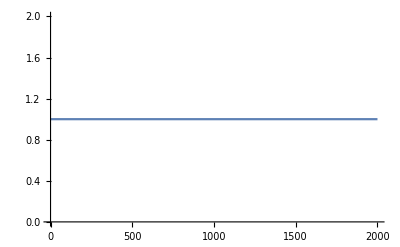
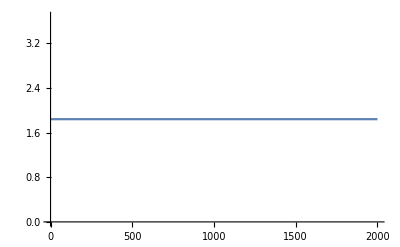
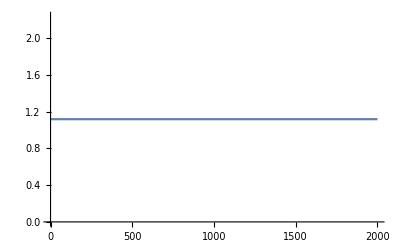
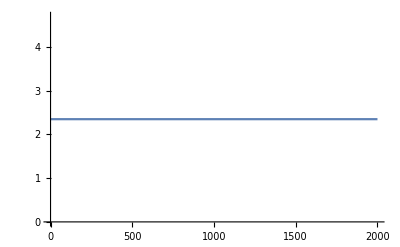
<|{2,1->2}→-Graphics-,{ex746,1->ex746}→-Graphics-,{3,2->3}→-Graphics-,{ex747,3->ex747}→-Graphics-,{2,en745->2}→-Graphics-,{1,1->2}→-Graphics-,{1,1->ex746}→-Graphics-,{2,2->3}→-Graphics-,{3,3->ex747}→-Graphics-,{en745,en745->2}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.

```mathematica
f=<|c->b|>
```

<|c→b|>

```mathematica
AssociateTo[f,v->m]
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
Append[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
AssociateTo[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m,m→b|>

```mathematica
f=Append[f,g->k]
```

<|c→b,v→m,m→b,g→k|>

```mathematica
f
```

<|c→b,v→m,m→b,g→k|>

```mathematica
Reduce[j589==0.+1. j589&&j589==0.+1. j589]
```

True

```mathematica
Solve[x^3 ==1, Reals]
```

{{x→1}}

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

$Aborted